```mathematica
ClearAll["Global`*"]

(*Interval Lengths a, b*) 
a=1;
b=6 ;
(*Central and sigma value for N1*)
σ = 0.4;

randomGen = 0;
P0  =1/(b-a);



Monitor[
While [ randomGen≤5,
μ=RandomReal[{a, b}];




rescalingFact = P0 *Sqrt[2π]σ;

N1 = rescalingFact * PDF[NormalDistribution[μ, σ], x];

rescFact2 =1/(P0(b-a) - NIntegrate[N1, {x, a, b}]);
PDF2 =  rescFact2 *(P0- N1);



PD2=ProbabilityDistribution[PDF2,{x,a,b}];
data=RandomVariate[PD2,10^5];



p=Show[
Histogram[data,80,"ProbabilityDensity"],
Plot [{ P0-N1,PDF2}, {x, a, b}, PlotRange->{{a, b}, {0, P0*rescFact2}}, PlotLegends->"Expressions", PlotStyle->Thick]
, ImageSize->Large];

Print[rescFact2];
Print[P0];

Print["Hitting space @ ", μ];


Pause[2];


randomGen++;

	]
, p]
```

```mathematica
probUnifom[x_, xmin_, xmax_]:=HeavisideTheta[x-xmin] HeavisideTheta[xmax-x];
probUniformNeg[x_, xmin_, xmax_, a_, b_]:=probUnifom[x, a, xmin] + probUnifom[x, xmax, b];
```

1.61011  1.31011  1.91011

0.262988 HeavisideTheta[6-x] HeavisideTheta[-1+x] (HeavisideTheta[6-x] HeavisideTheta[-1.91011+x]+HeavisideTheta[1.31011-x] HeavisideTheta[-1+x]) (HeavisideTheta[6-x] HeavisideTheta[-5.85237+x]+HeavisideTheta[5.25237-x] HeavisideTheta[-1+x])

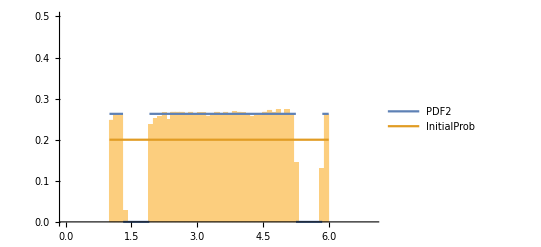

1.

```mathematica
(*Interval Lengths a, b*) 
a=1;
b=6 ;
(*Central and sigma value for N1*)
σ = 0.3;

P0  =1/(b-a);
μ=RandomReal[{a, b}];
Print[μ,"  ",  μ-σ,"  ",  μ+σ]

InitialProb =1/(b-a)*probUnifom[x,a, b];
DentingProb =  probUniformNeg[x, μ-σ, μ+σ, a, b];

rescFact2 =(b-a)/(b-a-2σ);


μ2=RandomReal[{a, b}];
DentingProb2 =  probUniformNeg[x, μ2-σ, μ2+σ, a, b];


newArea =Quiet[ NIntegrate[rescFact2*InitialProb * DentingProb*DentingProb2, {x, 1, b}]];

rescFact3 = 1/newArea;


PDF2=rescFact3*rescFact2*InitialProb * DentingProb*DentingProb2

PD2=ProbabilityDistribution[PDF2,{x,a,b}];
data=RandomVariate[PD2,10^5];

Show[
Histogram[data,50,"ProbabilityDensity",  PlotRange->{{a-1, b+1}, {0, 0.5}}],
Plot[{ PDF2, InitialProb}, {x,a,b}, PlotStyle->Thick, PlotLegends->"Expressions", PlotRange->{{a-1, b+1}, {0, 0.5}}, Epilog->Line[{{μ,0},{μ,100}}] ]
]

Quiet[ NIntegrate[rescFact3*rescFact2*InitialProb * DentingProb*DentingProb2, {x, 1, b}]]
```